physical constant

```mathematica
e=4.8*10^(-10);(*esu*)
me=9.1*10^(-28);(*g*)
mp=1.7*10^(-24);(*g*)
c=3*10^10;(*cm/s*)
pc=3.09*10^(18);(*cm*)
year=3600*24*365;(*s*)
day=3600*24;
hr=3600;
Rsun=7*10^(10);(*cm*)
Msun=2*10^(33);(*g*)
AU=1.5*10^13;(*cm*)
GHz=10^9;
G=6.7*10^(-8);(*erg cm g-2*)
h=6.6*10^(-27);(* erg s*)
hbar=h/(2Pi);
eV=1.6*10^(-12);
alphaF=1/137;
Jy=10^(-23);(*erg S-1 Hz cm-2*)
```

HMCB

-42559.5

3.62577

-Graphics-

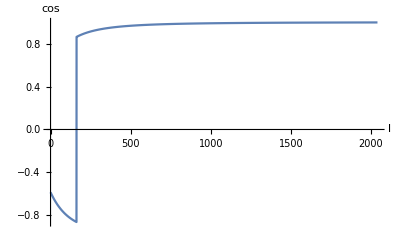

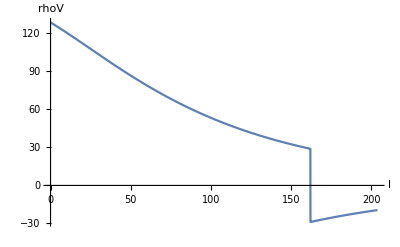

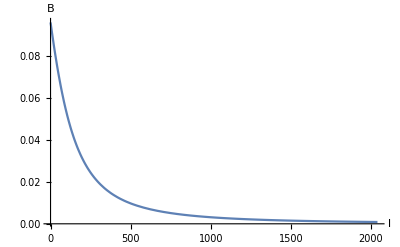

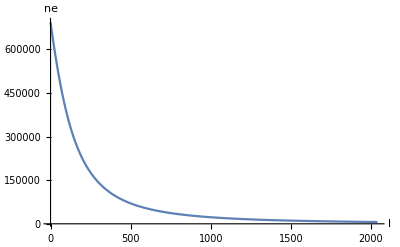

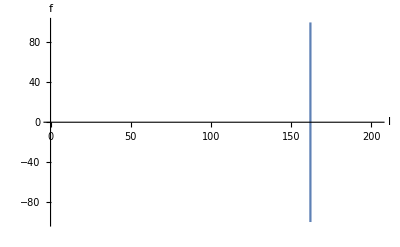

```mathematica
R1=Ri;
R2=Rf;
RMT[1]
DMT[1]
l0=-Ry/((Cos[Pi/2-phiO])*Cos[Pi/2-thetaO]);
Plot[{ Vsol[l] },{l,R1,R2}, GridLines->{{l0},{}},  PlotLegends->"Expressions",AxesOrigin->{0,0},AxesLabel->{"l","V"},PlotRange->{-1,1}]

Plot[{Cos[theta]},{l,R1,R2},GridLines->{{l0},{}},   PlotLegends->"Expressions",AxesOrigin->{0,0},AxesLabel->{"l","cos"},PlotRange->All]
Plot[{rhoVz},{l,R1,R2/10},GridLines->{{l0},{}},   PlotLegends->"Expressions",AxesOrigin->{0,0},AxesLabel->{"l","rhoV"},PlotRange->All]
Plot[{B[RxOb,RyOb,RzOb]},{l,R1,R2},  GridLines->{{l0},{}}, PlotLegends->"Expressions",AxesOrigin->{0,0},AxesLabel->{"l","B"},PlotRange->All]
Plot[{ne[RxOb,RyOb,RzOb]},{l,R1,R2},  GridLines->{{l0},{}}, PlotLegends->"Expressions",AxesOrigin->{0,0},AxesLabel->{"l","ne"},PlotRange->All]
Plot[{rhoVz/rhoQz},{l,R1,R2/10},GridLines->{{l0},{}},   PlotLegends->"Expressions",AxesOrigin->{0,0},AxesLabel->{"l","f"},PlotRange->{-100,100}]
```

```mathematica
ClearAll;
Remove[nn,Rorb,Rc,Bc,N0,thetac,thetacT,thetaorb,Rx,Ry,Rz,ne,Bp,Rs,u,ns,n0,x,y,z,r,xx,yy,zz,Bxx,Byy,Bzz,Bx,By,Bz,B,v,phiB,vp,vB,X,Y,theta,deltak1,rhoQ,rhoU,rhoV,a,rhoQz,rhoUz,rhoVz,Q,U,V,Qsol,Usol,Vsol,QsolT,UsolT,VsolT,RMT,DMT,thetaZT,phimu,thetamu,thetaYT,phi,BxT,ByT,l,phiT,phiOb,thetaOb,thetaob0,thetaFCT,phase,n1,n2,vT]

phiO=Pi/2;(*phi_L*)
thetaO=3Pi/12;(*theta_L*)
Vi=1;(*initial CP*)

(*Orbital Parameter*)
Rorb=204;
Rs=6;


(*environment*)
Bp=1000/9;
u=Bp*Rs^2;

ns=8*10^8;
N0=ns*Rs^2;

(*initial phi_orb*)
thetaorb0=-(Pi-phiO)+(0.5)*2Pi;

nn=200;n=0;
While[n<nn+1,n++;

Porb=100;
Pc=200;

alpha0=0Pi/12;(*alpha*)
thetaOmega0=3Pi/12;(*theta_Omega*)
ff=4;

thetaorb=thetaorb0+2Pi*n/nn*ff;(*orbital phase*)



phi=0.+2Pi*n/nn*Porb/Pc*ff;(*spin phase*)

thetaOb=(Pi-phiO)+thetaorb;
ROb=Rorb*Cos[Pi-thetaOb];
(*Location of Neutron star*)
Ry=Rorb*Sin[thetaorb];
Rx=Rorb*Cos[thetaorb];
Rz=0;




(*
alpha=alpha0;
thetaOmega=thetaOmega0;
cosphimu=(Cos[alpha]Sin[thetaOmega]+Sin[alpha]Cos[thetaOmega]Cos[phi])/((Sin[alpha]Sin[phi])^2+(Cos[alpha]Sin[thetaOmega]+Sin[alpha]Cos[thetaOmega]Cos[phi])^2)^(1/2);
sinphimu=(Sin[alpha]Sin[phi])/((Sin[alpha]Sin[phi])^2+(Cos[alpha]Sin[thetaOmega]+Sin[alpha]Cos[thetaOmega]Cos[phi])^2)^(1/2);
costhetamu=Cos[alpha]Cos[thetaOmega]-Sin[alpha]Sin[thetaOmega]Cos[phi];

sinthetamu=Sin[alpha]Sin[phi]/sinphimu;
CosthetaY=costhetamu;
SinthetaY=sinthetamu;
CosthetaZ=cosphimu;
SinthetaZ=sinphimu;
*)
(*coordinate transformation*)
alpha=alpha0;
thetaOmega=thetaOmega0;

mux=Cos[alpha0]Sin[thetaOmega0]-Sin[alpha0]Cos[thetaOmega0]Cos[phi];
muy=-Sin[alpha0]Sin[phi];
muz=Cos[alpha0]Cos[thetaOmega0]+Sin[alpha0]Sin[thetaOmega0]Cos[phi];

phimu=ArcTan[mux,muy];
thetamu=ArcTan[muz,Sqrt[mux^2+muy^2]];
CosthetaY=Cos[thetamu];
SinthetaY=Sin[thetamu];
CosthetaZ=Cos[phimu];
SinthetaZ=Sin[phimu];


(*phimu=0.0001;
thetamu=0.001;*)


v=1;(*GHz*)
rotaionM1={CosthetaY *CosthetaZ,-CosthetaY*SinthetaZ,SinthetaY};
rotaionM2={SinthetaZ,CosthetaZ,0};
rotaionM3={-CosthetaZ* SinthetaY,SinthetaY* SinthetaZ,CosthetaY};
xx=Dot[rotaionM1,{x,y,z}];
yy=Dot[rotaionM2,{x,y,z}];
zz=Dot[rotaionM3,{x,y,z}];
r=(xx^2+yy^2+zz^2)^(1/2);
(*B'*)
Bxx=Tanh[1000000zz]*u/(r^2)*xx/r;
Byy=Tanh[1000000zz]*u/(r^2)*yy/r;
Bzz=Tanh[1000000zz]*u/(r^2)*zz/r;

(*B*)
rotaionMT1={CosthetaY* CosthetaZ,SinthetaZ,-CosthetaZ* SinthetaY};
rotaionMT2={-CosthetaY* SinthetaZ,CosthetaZ,SinthetaY*SinthetaZ};
rotaionMT3={SinthetaY,0,CosthetaY};
Bxyz={Bxx,Byy,Bzz};
Bx[x_,y_,z_]=Dot[rotaionMT1,Bxyz];
By[x_,y_,z_]=Dot[rotaionMT2,Bxyz];
Bz[x_,y_,z_]=Dot[rotaionMT3,Bxyz];
(*Bx[x_,y_,z_]=u/(r^2)*x/r;
By[x_,y_,z_]=u/(r^2)*y/r;
Bz[x_,y_,z_]=u/(r^2)*z/r;*)
B[x_,y_,z_]=(Bx[x,y,z]^2+By[x,y,z]^2+Bz[x,y,z]^2)^(1/2);
ne[x_,y_,z_]=N0*r^(-2);

RxOb=Rx+(l)*Sin[thetaO]Cos[phiO];
RyOb=Ry+(l)*Sin[thetaO]Sin[phiO];
RzOb=Rz+(l)*Cos[thetaO];


phiB=0;
vp=(4*Pi*e^2*ne[RxOb,RyOb,RzOb]/me)^(1/2)/(2Pi)/GHz;
vB=e*B[RxOb,RyOb,RzOb]/(me*c)/(2Pi)/GHz;
X=vp^2/v^2;
Y=vB/v;
theta=ArcCos[Dot[{Bx[RxOb,RyOb,RzOb],By[RxOb,RyOb,RzOb],Bz[RxOb,RyOb,RzOb]},{Sin[thetaO]Cos[phiO],Sin[thetaO]Sin[phiO],Cos[thetaO]}]/B[RxOb,RyOb,RzOb]];


deltak1=(2Pi*v*GHz/c)*X*Y*Rsun;
(*deltak1[x_,y_,z_]:=(2Pi*v*GHz/c)*X[x,y,z]*Y[x,y,z]/(1-X[x,y,z]-Y[x,y,z]^2+X[x,y,z]Y[x,y,z]^2Cos[theta[x,y,z]]^2)*Rsun;*)
rhoQ=-deltak1*Y/2*Sin[theta]^2*Cos[2phiB];

rhoU=-deltak1*Y/2*Sin[theta]^2*Sin[2phiB];
(*rhoV[x_,y_,z_]:=-deltak1[x,y,z]*(1-X[x,y,z])*Cos[theta[x,y,z]];*)
rhoV=-deltak1*Cos[theta];
(*rhoV1[x_,y_,z_]:=-deltak1[x,y,z]*(1-X[x,y,z]);*)


Ri=0;
Rf=10Rorb;
(*微分方程*)
rhoQz=rhoQ;
rhoUz=rhoU;
rhoVz=rhoV;
(*{Qsol,Usol,Vsol}=NDSolveValue[{Q'[l]+rhoVz*U[l]-rhoUz*V[l]==0,U'[l]-rhoVz*Q[l]+rhoQz*V[l]==0,V'[l]+rhoUz*Q[l]-rhoQz*U[l]==0,Q[Ri]==0,U[Ri]==Sqrt[1-Vi^2],V[Ri]==Vi},{Q,U,V},{l,Ri,Rf},MaxSteps->10^8];
QsolT[n]=Qsol[Rf];
UsolT[n]=Usol[Rf];
VsolT[n]=Vsol[Rf];*)
vT[n]=v;
phase[n]=thetaorb/(2Pi);(*phi_orb*)
RMT[n]=-NIntegrate[rhoVz,{l,Ri,3Rf},PrecisionGoal->2,MaxRecursion->20,Method->"LocalAdaptive"]/(2(c/(v*GHz)/100)^2);
DMT[n]=NIntegrate[ne[RxOb,RyOb,RzOb],{l,Ri,3Rf},PrecisionGoal->2,MaxRecursion->20,Method->"LocalAdaptive"]/(pc/Rsun);
]//AbsoluteTiming
```

{1.96214,Null}

RM

```mathematica
Export["RMHMXBP200a0.dat",Table[{phase[n]+0.5,RMT[n]},{n,1,nn}]];
```

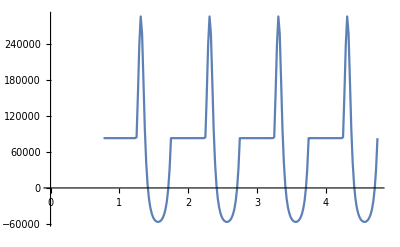

```mathematica
ListPlot[{Table[{phase[n]+0.5,RMT[n]},{n,0,nn}]},Joined->True]
```

DM

```mathematica
Export["DMHMXBPorb.dat",Table[{phase[n]+0.5,DMT[n]},{n,1,nn}]];
```

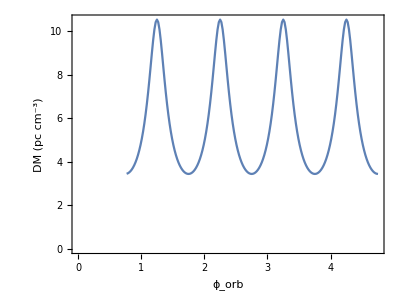

```mathematica
ListPlot[{Table[{phase[n]+0.5,DMT[n]},{n,0,nn}]},Joined->True,Frame->True,FrameLabel->{{Style["DM (pc cm^-3)",13],Null},{Style["ϕ_orb",13],Null}},FrameStyle->Black,LabelStyle->{GrayLevel[0],13,(FontFamily->"Times New Roman")},AspectRatio->3/4,PlotStyle->Automatic]
```

L,V

```mathematica
Export["VfHMXBPorb.dat",Table[{phase[n]+0.5,0.5*VsolT4[n]},{n,1,nn}]];
Export["LfHMXBPorb.dat",Table[{phase[n]+0.5,Sqrt[1-(0.5*VsolT4[n])^2]},{n,1,nn}]];
```

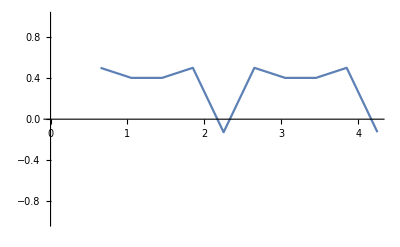

```mathematica
ListPlot[{Table[{phase[n]+0.5,0.5*VsolT[n]},{n,0,nn}]},Joined->True,PlotRange->{-1,1}]
```

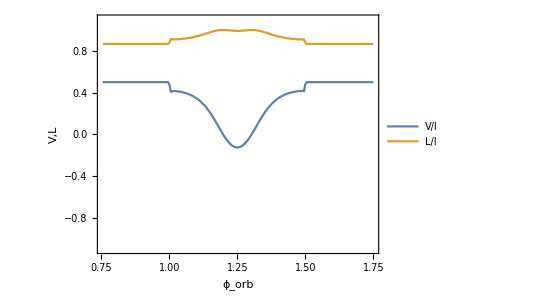

```mathematica
ListPlot[{Import["VfHMXBPorb.dat"],Import["LfHMXBPorb.dat"]},Frame->True,FrameLabel->{{Style["V,L",13,Italic],Null},{Style["ϕ_orb",13],Null}},FrameStyle->Black,LabelStyle->{GrayLevel[0],13,(FontFamily->"Times New Roman")},AspectRatio->3/4,PlotStyle->Automatic,PlotRange->{All,{-1.1,1.1}},PlotLegends->Placed[LineLegend[{Style["V/I",13],Style["L/I",13]},LegendLayout->"Column"],{Scaled[{0.65,0.05}],{0,0}}],PlotStyle->{Purple,Red,Black,Blue,Orange},Joined->True]
```

LMCB

```mathematica
ClearAll;
Remove[nn,Rorb,Rc,Bc,N0,thetac,thetacT,thetaorb,Rx,Ry,Rz,ne,Bp,Rs,u,ns,n0,x,y,z,r,xx,yy,zz,Bxx,Byy,Bzz,Bx,By,Bz,B,v,phiB,vp,vB,X,Y,theta,deltak1,rhoQ,rhoU,rhoV,a,rhoQz,rhoUz,rhoVz,Q,U,V,Qsol,Usol,Vsol,QsolT,UsolT,VsolT,RMT,DMT,thetaZT,phimu,thetamu,thetaYT,phi,BxT,ByT,l,phiT,phiOb,thetaOb,thetaob0,thetaFCT,phase,n1,n2]

phiO=Pi/2;(*phi_L*)
thetaO=3Pi/12;(*theta_L*)
Vi=1;(*initial CP*)

(*Orbital Parameter*)
Rorb=18;
Rs=0.5;


(*environment*)
Bp=1000;
u=Bp*Rs^3;

ns=8*10^4;
N0=ns*Rs^2;

thetac=0+0.5*2Pi;
(*initial phi_orb*)
thetaorb0=-(Pi-phiO)+thetac;

nn=100;n=0;
(*循环*)
While[n<nn+1,n++;

Porb=5;
Pc=10;

alpha0=5Pi/12;(*alpha*)
thetaOmega0=0;(*theta_Omega*)
ff=5;

thetaorb=thetaorb0+2Pi*n/nn*ff;(*orbital phase*)



phi=0.+2Pi*n/nn*Porb/Pc*ff;(*spin phase*)


thetaOb=(Pi-phiO)+thetaorb;
ROb=Rorb*Cos[Pi-thetaOb];
(*Location of Neutron star*)
Ry=Rorb*Sin[thetaorb];
Rx=Rorb*Cos[thetaorb];
Rz=0;





(*
alpha=alpha0;
thetaOmega=thetaOmega0;
cosphimu=(Cos[alpha]Sin[thetaOmega]+Sin[alpha]Cos[thetaOmega]Cos[phi])/((Sin[alpha]Sin[phi])^2+(Cos[alpha]Sin[thetaOmega]+Sin[alpha]Cos[thetaOmega]Cos[phi])^2)^(1/2);
sinphimu=(Sin[alpha]Sin[phi])/((Sin[alpha]Sin[phi])^2+(Cos[alpha]Sin[thetaOmega]+Sin[alpha]Cos[thetaOmega]Cos[phi])^2)^(1/2);
costhetamu=Cos[alpha]Cos[thetaOmega]-Sin[alpha]Sin[thetaOmega]Cos[phi];

sinthetamu=Sin[alpha]Sin[phi]/sinphimu;

CosthetaY=costhetamu;
SinthetaY=sinthetamu;
CosthetaZ=cosphimu;
SinthetaZ=sinphimu;*)

(*coordinate transformation*)
alpha=alpha0;
thetaOmega=thetaOmega0;

mux=Cos[alpha0]Sin[thetaOmega0]-Sin[alpha0]Cos[thetaOmega0]Cos[phi];
muy=-Sin[alpha0]Sin[phi];
muz=Cos[alpha0]Cos[thetaOmega0]+Sin[alpha0]Sin[thetaOmega0]Cos[phi];

phimu=ArcTan[mux,muy];
thetamu=ArcTan[muz,Sqrt[mux^2+muy^2]];

CosthetaY=Cos[thetamu];
SinthetaY=Sin[thetamu];
CosthetaZ=Cos[phimu];
SinthetaZ=Sin[phimu];


(*phimu=0.0001;
thetamu=0.001;*)

v=1;(*GHz*)
rotaionM1={CosthetaY *CosthetaZ,-CosthetaY*SinthetaZ,SinthetaY};
rotaionM2={SinthetaZ,CosthetaZ,0};
rotaionM3={-CosthetaZ* SinthetaY,SinthetaY* SinthetaZ,CosthetaY};
xx=Dot[rotaionM1,{x,y,z}];
yy=Dot[rotaionM2,{x,y,z}];
zz=Dot[rotaionM3,{x,y,z}];
r=(xx^2+yy^2+zz^2)^(1/2);
(*B'*)
Bxx=u/(2r^3)*(3xx/r)*zz/r;
Byy=u/(2r^3)*(3yy/r)*zz/r;
Bzz=u/(2r^3)*(3(zz/r)^2-1);

(*B*)
rotaionMT1={CosthetaY* CosthetaZ,SinthetaZ,-CosthetaZ* SinthetaY};
rotaionMT2={-CosthetaY* SinthetaZ,CosthetaZ,SinthetaY*SinthetaZ};
rotaionMT3={SinthetaY,0,CosthetaY};
Bxyz={Bxx,Byy,Bzz};
Bx[x_,y_,z_]=Dot[rotaionMT1,Bxyz];
By[x_,y_,z_]=Dot[rotaionMT2,Bxyz];
Bz[x_,y_,z_]=Dot[rotaionMT3,Bxyz];
B[x_,y_,z_]=(Bx[x,y,z]^2+By[x,y,z]^2+Bz[x,y,z]^2)^(1/2);
ne[x_,y_,z_]=N0*r^(-2);



RxOb=Rx+(l)*Sin[thetaO]Cos[phiO];
RyOb=Ry+(l)*Sin[thetaO]Sin[phiO];
RzOb=Rz+(l)*Cos[thetaO];


phiB=0;
vp=(4*Pi*e^2*ne[RxOb,RyOb,RzOb]/me)^(1/2)/(2Pi)/GHz;
vB=e*B[RxOb,RyOb,RzOb]/(me*c)/(2Pi)/GHz;
X=vp^2/v^2;
Y=vB/v;
theta=ArcCos[Dot[{Bx[RxOb,RyOb,RzOb],By[RxOb,RyOb,RzOb],Bz[RxOb,RyOb,RzOb]},{Sin[thetaO]Cos[phiO],Sin[thetaO]Sin[phiO],Cos[thetaO]}]/B[RxOb,RyOb,RzOb]];
thetaT[n]=theta;

deltak1=(2Pi*v*GHz/c)*X*Y*Rsun;
(*deltak1[x_,y_,z_]:=(2Pi*v*GHz/c)*X[x,y,z]*Y[x,y,z]/(1-X[x,y,z]-Y[x,y,z]^2+X[x,y,z]Y[x,y,z]^2Cos[theta[x,y,z]]^2)*Rsun;*)
rhoQ=-deltak1*Y/2*Sin[theta]^2*Cos[2phiB];

rhoU=-deltak1*Y/2*Sin[theta]^2*Sin[2phiB];
(*rhoV[x_,y_,z_]:=-deltak1[x,y,z]*(1-X[x,y,z])*Cos[theta[x,y,z]];*)
rhoV=-deltak1*Cos[theta];
(*rhoV1[x_,y_,z_]:=-deltak1[x,y,z]*(1-X[x,y,z]);*)

Ri=0;
Rf=10Rorb;
rhoQz=rhoQ;
rhoUz=rhoU;
rhoVz=rhoV;



{Qsol,Usol,Vsol}=NDSolveValue[{Q'[l]+rhoVz*U[l]-rhoUz*V[l]==0,U'[l]-rhoVz*Q[l]+rhoQz*V[l]==0,V'[l]+rhoUz*Q[l]-rhoQz*U[l]==0,Q[Ri]==0,U[Ri]==Sqrt[1-Vi^2],V[Ri]==Vi},{Q,U,V},{l,Ri,Rf},MaxSteps->10^8];

QsolT[n]=Qsol[Rf];
UsolT[n]=Usol[Rf];
VsolT[n]=Vsol[Rf];
vT[n]=v;
phase[n]=thetaorb/(2Pi);(*phi_orb*)
RMT[n]=-NIntegrate[rhoVz,{l,Ri,3Rf},PrecisionGoal->10,MaxRecursion->20]/(2(c/(v*GHz)/100)^2);
DMT[n]=NIntegrate[ne[RxOb,RyOb,RzOb],{l,Ri,3Rf},PrecisionGoal->5,MaxRecursion->20]/(pc/Rsun);
]//AbsoluteTiming
```

{1.90302,Null}